# Horizontal motion

info@cafeplanck.com

```mathematica
ClearAll["Global`*"]
```

## Initiation

Mass :

```mathematica
m:=2
```

Acceleration of gravity :

```mathematica
g:=9.80665
```

Initial position :

```mathematica
Subscript[x, 0]:=-15
```

Initial horizontal velocity :

```mathematica
Subscript[v, 0]:=20
```

Horizontal force:

```mathematica
F:=-6
```

Resistance :

```mathematica
μ=0.2;
```

Friction force (N) :

```mathematica
f=Sign[-F]μ m g
```

3.92266

```mathematica
totalTime=10
```

10

## Differential equation with initial conditions

```mathematica
equ=m x''[t]==F-f;
```

```mathematica
cond1=x'[0]==Subscript[v, 0];
```

```mathematica
cond2=x[0]==Subscript[x, 0];
```

## DSolve

```mathematica
Off[Solve::ifun]
```

```mathematica
DS=DSolve[{equ,cond1,cond2},x[t],t]//FullSimplify
```

{{x[t]→-15.+(20.-2.48067 t) t}}

## Equation of motion

```mathematica
x[t_]=DS[[1,1,2]]
```

-15.+(20.-2.48067 t) t

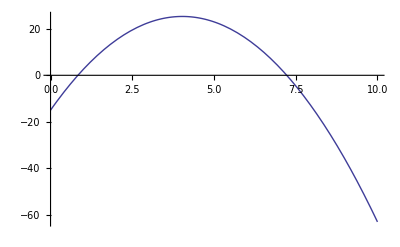

```mathematica
Plot[x[t],{t,0,totalTime}]
```

```mathematica
Solve[x[t]==0,t]//N
```

{{t→0.836866},{t→7.22549}}

## Equation of velocity

```mathematica
v[t_]=D[x[t],t]
```

20.-4.96133 t

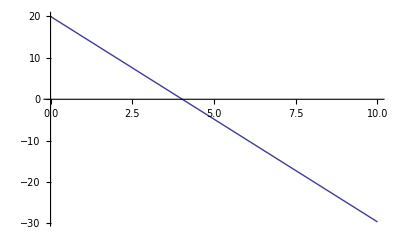

```mathematica
Plot[v[t],{t,0,totalTime}]
```

```mathematica
Solve[v[t]==0,t]//N
```

{{t→4.03118}}

## Equation of acceleration

```mathematica
a[t_]=D[v[t],t]
```

-4.96133

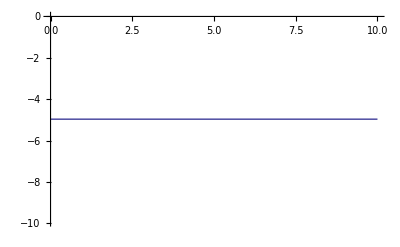

```mathematica
Plot[a[t],{t,0,totalTime}]
```

## NDSolve

```mathematica
Clear[x]
```

```mathematica
NDS:=NDSolve[{equ,cond1,cond2},x,{t,0,totalTime}]
```

## Animation

```mathematica
xRange:=30
```

```mathematica
Animate[
Graphics[{
Evaluate[PointSize[0.03],Red,Point[{x[t],0} /. NDS]]},
(*----------------*)
Axes->{True,False},
PlotLabel->Cases[NotebookGet[],Cell[t_,"Title",___]:>t,Infinity][[1]],
PlotRange->{{-xRange,xRange},{-3,3}}],
(*----------------*)
{t,0,totalTime},
AnimationRepetitions->1,
DefaultDuration->totalTime,
AnimationRunning->False]
```